# Solving Laplace’s Equation using Finite Differences and Finite Elements Matthew Peterson, Morgan Rivers, Julia Rowe, and Isabel Yannatos

## Solving Laplace’s Equation with Finite Differences

### Create the matrix representation of the finite difference Laplacian

Here we define the function laplace, which creates a matrix operator to perform the finite difference operation on the function θ.

```mathematica
laplace[numX_]:=Block[{mat,row,i,left,right},
(*define default matrix, without boundary conditions enforced*)
mat=Table[If[i==j,-4.,0.]+If[j+1==i,1.,0.]+If[j==i+1,1.,0.]+If[j-numX==i,1.,0.]+If[j+numX==i,1.,0.],{i,numX^2},{j,numX^2}];
(*enforce the boundary conditions along the top and bottom.*)
For[i=1,i≤numX,i++,
row=ConstantArray[0,numX^2];
row⟦i⟧=1;
mat⟦i⟧=row;
mat⟦numX^2-i+1⟧=Reverse[row];
];
(*allow for periodic boundary conditions along edges of matrix.*)
For[i=1,i≤numX-2,i++,
left=1+i*numX;
right=(i+1)*numX;
mat⟦left⟧=Table[If[left==j,-4.,0.]+If[left+numX-1==j,1.,0.]+If[left+1==j,1.,0.]+If[left+numX==j,1.,0.]+If[left-numX==j,1.,0.],{j,numX^2}];
mat⟦right⟧=Table[If[right==j,-4.,0.]+If[right-numX+1==j,1.,0.]+If[right-1==j,1.,0.]+If[right+numX==j,1.,0.]+If[right-numX==j,1.,0.],{j,numX^2}];
];
Return[mat];
];
```

### Solve Laplace’s equation

define solveLaplace, which solves Laplace’s equation on the patterned surface using a grid spacing of δ

```mathematica
solveLaplace[δ_]:=Block[{A,b,x,y,θ,size,boundaryConditions},
x=Range[0,1,δ];
y=Range[0,1,δ];
size=Length[x];
A=laplace[size];
b = ConstantArray[0.0,size^2];
(* create the boundary conditions along the top and bottom *)
boundaryConditions=Table[If[i≤size/2,π/2.0,0.0],{i,size}];
b⟦size^2-(size-1);;size^2⟧=boundaryConditions;
b⟦1;;size⟧=boundaryConditions;
(* solve the equation, and then return as a matrix *)
θ=ArrayReshape[LinearSolve[A,b],{size,size}];
Return[{θ,x,y}];
];
```

```mathematica
sol=solveLaplace[1./50];
```

```mathematica
ListPlot3D[sol⟦1⟧,BaseStyle->{FontName->"Helvetica",FontSize->14},AxesStyle->Black,PlotLegends->Automatic]
```

-Graphics3D-

## Measuring the Energy using Finite Differences

findEnergy determines the energy given a discretization size on the internal points using central difference for the gradient F=∫∫(∇θ)^2 dx dy

```mathematica
findEnergy[δ_]:=Block[{sol,F},
sol=solveLaplace[δ]⟦1⟧;
F=Table[((sol⟦i+1,j⟧-sol⟦i-1,j⟧)/(2δ))^2+((sol⟦i,j+1⟧-sol⟦i,j-1⟧)/(2δ))^2,{i,2,Length[sol]-1},{j,2,Length[sol]-1}];
F=Total[Flatten[F]] δ^2;
Return[F];
];
```

Find the energy using different discretization sizes to see if it converges

```mathematica
energy=Table[{1.0/k,findEnergy[1.0/k]},{k,5,50,5}];
```

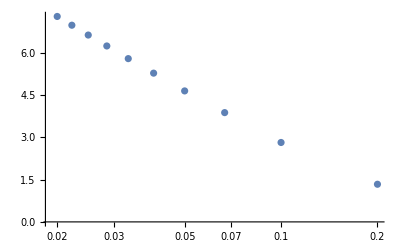

```mathematica
ListLogLinearPlot[energy]
```

Rather than converging, we actually see the energy increase exponentially. This actually makes sense, and is one of the results of using a continuous field theory to describe the liquid crystal alignment.

## Comparing Finite Differences with Analytical Solution

We will take the squared difference between the analytical and numerical solution and analyze the differences

```mathematica
θ[x_,y_]=Pi/4+Pi/2 Sum[-(((-1+(-1)^n) E^(-2 n π y) (E^(2 n π)+E^(4 n π y)) Sin[2 n π x])/((1+E^(2 n π)) n π)),{n,1,50,2}];
```

```mathematica
{Plot3D[θ[x,y,50],{x,0,1},{y,0,1},ImageSize->Medium],ListPlot3D[sol⟦1⟧,ImageSize->Medium]}
```

{-Graphics3D-,-Graphics3D-}

Notice that qualitatively, the finite difference and analytical solution match quite well.

findError will determine the mean error as we reduce the discretization size

```mathematica
findError[]:=Block[{δ,i,sol,error,θlist,data},
δ=Table[1.0/k,{k,5,50,2}];
error=ConstantArray[0,Length[δ]];
For[i=1,i≤Length[δ],i++,
sol=solveLaplace[δ⟦i⟧];
θlist=Table[θ[sol⟦2⟧⟦j⟧,sol⟦3⟧⟦i⟧],{i,1,Length[sol⟦2⟧]},{j,1,Length[sol⟦3⟧]}];
error⟦i⟧=Sqrt[Mean[Flatten[(θlist-sol⟦1⟧)^2]]];
];
data=Table[{δ⟦i⟧,error⟦i⟧},{i,1,Length[δ]}];
Return[data];
];
```

```mathematica
error=findError[];
```

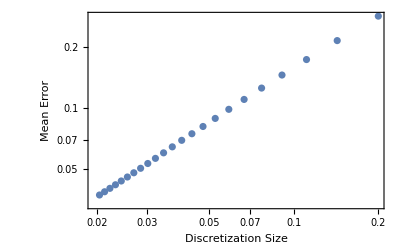

```mathematica
ListLogLogPlot[error,Frame->True,FrameLabel->{"Discretization Size","Mean Error"},BaseStyle->{FontName->"Helvetica",FontSize->14}]
```

The error shows a clear decrease as we increase the discretization size (as it should), which shows linear behavior on a log-log scale

Now we attempt to fit the error to find the order of accuracy

```mathematica
logError=Table[{Log[error⟦i,1⟧],Log[error⟦i,2⟧]},{i,Length[error]}];
```

{a→0.900454,b→0.222077}

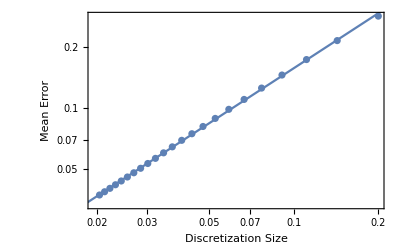

```mathematica
model=a x + b;
fit = FindFit[logError,model,{a,b},x]
Show[ListLogLogPlot[error,Frame->True,FrameLabel->{"Discretization Size","Mean Error"},BaseStyle->{FontName->"Helvetica",FontSize->14}],Plot[model/.fit,{x,-10,10}]]
```

The error is fit very well to an equation of the form error ≃δ^0.90, showing accuracy almost on the order of the discretization size (though not quite)

## Solving Laplace’s Equation with Finite Elements

Consider first Laplace’s equation in 2D, ∇^2 u(x,y)=0, and let v_i(x,y) be test functions such that u(x,y)=∑_i u_i v_i(x,y). Then ∫v_i∇^2 u dΩ=v_i u_j∇v_j·n̂|_Γ-∫(∇v_i·∇v_j )u_j dΩ=0. The first term drops to zero, as we don’t expect “flow” into or out of our domain, and Dirichlet boundary conditions are specified in the construction of the second term. Thus, we are left with
 						∫dΩ (∇v_i·∇v_j)u_i=0→ Lu=0 where L_ij=∫dΩ (∇v_i·∇v_j) 
 for all internal points. If the vertex i is specified as having the value u_i, then to enforce this boundary condition we let L_ij=δ_ij for the row i corresponding to the fixed value u_i.

We first define a few useful quantities:
	- n: the width (and height) in number of grid points of our discretized region
	- mesh: the Delaunay mesh itself
	- coords: the coordinates of each mesh point
	- triangles: the mesh indices describing each triangle in the mesh
	- leftBounds: the indices of points on the left boundary
	- rightBounds: the indices of points on the right boundary
note that coords⟦triangles⟦i⟧⟧ gives the coordinate positions for each point in triangle i, which can be used to calculate the gradiants, inner products, etc

```mathematica
n=15;
mesh=DelaunayMesh[Flatten[Table[{(i-1)/(n-1),(j-1)/(n-1)},{i,n},{j,n}],1]];
coords=MeshCoordinates[mesh];
triangles=MeshCells[mesh,2]⟦All,1⟧;
leftBounds=Table[1+(i-1) n,{i,1,n}];
rightBounds=Table[i n, {i, 1, n}];
```

findTriangles can determine the triangles attached to the mesh vertex idx based on the vertices defining each triangle

```mathematica
findTriangles[idx_]:=triangles⟦Position[Map[Apply[MemberQ],Table[{triangles⟦i⟧,idx},{i,1,Length[triangles]}]],True]⟦All,1⟧⟧;
```

triangleArea⟦triangles⟦i⟧⟧ gives the area of the ith triangle

```mathematica
triangleArea[triangle_]:=Block[{pts,θ,vec1,vec2},
pts=coords⟦triangle⟧;
(*Convert to float by multiplying by 1.0, this speeds up calculations tremendously*)
vec1=1.0(pts⟦2⟧-pts⟦1⟧);
vec2=1.0(pts⟦3⟧-pts⟦1⟧);
θ=VectorAngle[vec1,vec2];
Return[0.5 Norm[vec1]Norm[vec2]Sin[θ]];
];
```

gradPlane calculates the gradient of the plane created by the witches hat function on the triangle triangle with the index center as the point of the triangle with z=1 (all other points have z=0)

```mathematica
gradPlane[triangle_,center_]:=Block[{pos,triCoords,centerCoord,normal,vec,i},
triCoords=coords⟦triangle⟧;
centerCoord=Position[triangle,center]⟦All,1⟧⟦1⟧;
pos=Table[0,{i,3},{j,3}];

(*Construct the plane from the three points in the triangle*)
For[i=1,i≤3,i++,
pos⟦i,1;;2⟧=triCoords⟦i⟧;
If[i==centerCoord,pos⟦i,3⟧=1,pos⟦i,3⟧=0]
];
vec[1]=1.0(pos⟦2⟧-pos⟦1⟧);
vec[2]=1.0(pos⟦3⟧-pos⟦1⟧);

(*Find the gradient*)
normal=Cross[vec[1],vec[2]];
normal=1.0(normal/(-normal⟦3⟧));
Return[normal⟦1;;2⟧];
];
```

innerGradProduct[i, j] calculates the inner product of the gradients of v_i and v_j: ⟨∇v_i,∇v_j⟩=∫∇v_i·∇v_jdΩ

```mathematica
innerGradProduct[i_,j_]:=Block[{sum,sharedTriangles,triangle,k,viCoord,vjCoord},
sharedTriangles=Intersection[findTriangles[i],findTriangles[j]];
sum=0.0;
(*if no shared triangles,return an inner gradient of zero*)
If[sharedTriangles=={},
Return[sum],
For[k=1,k≤Length[sharedTriangles],k++,
triangle=sharedTriangles⟦k⟧;
viCoord=i;
vjCoord=j;
(*Sum the inner product of the gradient for each shared triangles*)
sum=sum+1.0×gradPlane[triangle,viCoord].gradPlane[triangle,vjCoord]×triangleArea[triangle];
];
];
Return[sum];
];
```

Constructs the matrix, and defines it such that the corners allow for boundary conditions (using identity matrices in the top left and bottom right NxN sub-matrices)

```mathematica
constructMatrix[]:=Block[{A,i,row,left,right,b},
(* create the initial matrix (ignoring boundary conditions) *)
A=Table[innerGradProduct[i,j],{i,n^2},{j,n^2}];

b=ConstantArray[0,n^2];
b⟦1;;n⟧=Table[If[i≤n/2,π/2,0],{i,1,n}];
b⟦n^2-n+1;;n^2⟧=Table[If[i≤n/2,π/2,0],{i,1,n}];

(*Enforce boundary conditions*)
For[i=1,i≤n,i++,
row=ConstantArray[0,n^2];
row⟦i⟧=1;
A⟦i⟧=row;
A⟦n^2-i+1⟧=Reverse[row];
];

(* Fix periodic boundary conditions. We do this by letting the left boundary be effectively the same as the right, so for the row of the matrix corresponding to the right boundary, we add the row corresponding to the left boundary so that the points are connected. We then replace the row corresponding to the left boundary with the condition that θleft - θright = 0, to enforce equality *)
For[i=2,i≤Length[leftBounds]-1,i++,
left=leftBounds⟦i⟧;
right=rightBounds⟦i⟧;
A⟦right⟧=A⟦left⟧+A⟦right⟧;
A⟦left⟧=ConstantArray[0,n^2];
A⟦left,left⟧=1;
A⟦left,right⟧=-1;
];
Return[{A,b}];
];
```

```mathematica
A=constructMatrix[];
```

```mathematica
solFEM=ArrayReshape[LinearSolve[A⟦1⟧,A⟦2⟧],{n,n}];
```

```mathematica
ListPlot3D[solFEM]
```

-Graphics3D-

## Comparing Finite Differences with Finite Elements and the Analytical Solution

```mathematica
dx=1.0/14.0;
```

```mathematica
solFD=solveLaplace[dx]⟦1⟧;
```

```mathematica
{ListPlot3D[solFEM,ImageSize->Medium],ListPlot3D[solFD,ImageSize->Medium]}
```

{-Graphics3D-,-Graphics3D-}

Qualitatively, the two methods give very similar results. Close examination reveals some differences, however, especially at boundaries

```mathematica
solAna=Table[θ[(j-1)dx,(i-1) dx],{i,15},{j,15}];
```

```mathematica
{errorFEM=Sqrt[Mean[Flatten[(solAna-solFEM)^2]]],errorFD=Sqrt[Mean[Flatten[(solAna-solFD)^2]]]}
```

{0.141566,0.150077}

Cursory inspection shows similar error in both the finite elements and finite difference methods. Unfortunately, the finite elements method proved to be unusably slow for anything beyond a 15x15 grid size (the time seems to scale as N^6 for an N×N grid). This made it difficult to do any useful comparison of the methods, as the error is still large at these grid sizes. As it is implemented, the finite difference is actually the better method due purely to the faster solutions times with significantly larger grids (we tested grids as large as 50x50, though larger is quite possible). These larger grids reduced the error considerably. However, an optimized finite elements method may prove to be better in the end.